### Question 6

Part a:

```mathematica
x /.NSolve[x^8-4 x^3==3,x] //TableForm
```

-1.06168-0.849585 ⅈ
-1.06168+0.849585 ⅈ
-0.873104
0.304089-1.22508 ⅈ
0.304089+1.22508 ⅈ
0.500853-0.768325 ⅈ
0.500853+0.768325 ⅈ
1.38658

Part b:

```mathematica
Clear["Global`*"]
```

```mathematica
sqrt = Table[Sqrt[n], {n,10^6,1.5 10^6}];
```

```mathematica
Length[Select[sqrt,IntegerQ]]
```

225

Part c :

```mathematica
Integrate[(1+x^n)^-m,{x,0,Infinity}, Assumptions->{m>0, n>0, m n>1}]
```

(Gamma[m-1/n] Gamma[1+1/n])/Gamma[m]

For the case of m=1:

```mathematica
Integrate[(1+x^n)^-1,{x,0,Infinity}, Assumptions->{n>1}]
```

(π Csc[π/n])/n

### Question 7

```mathematica
h=0.001; J=1;
```

Part a:

```mathematica
T=1;
```

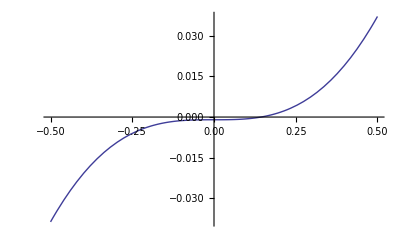

```mathematica
Plot[m==Tanh[(J m + h) / T], {m, -.5, .5}]
```

The function was plotted in order to identify where to locate the root of the function.

```mathematica
sol = m/.FindRoot[{m==Tanh[(h+m)/T]},{m,1}][[1]]
```

0.143626

Part b:

```mathematica
Clear["Global`*"];
```

```mathematica
sol := m/.FindRoot[{m==Tanh[(h+m)/T]},{m,1}][[1]]
```

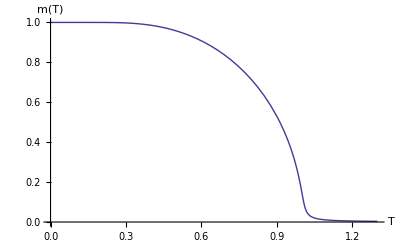

```mathematica
Plot[{sol}, {T, 0, 1.3}, AxesLabel-> {"T", "m(T)"}]
```

### Question 8

```mathematica
λ := 9/10
```

```mathematica
f[x_]:=4 λ x (1 - x);
```

Part a:

```mathematica
lyapunov[xinit_, n_, ninitialize_] := (xlist = Drop[NestList[f, xinit, n], ninitialize+1]; Apply[Plus, Log[Abs[f'[xlist]]]]/Length[xlist])
```

```mathematica
lyapunov[0.5, 50000, 20]
```

0.182963

Part b:

```mathematica
x0=N[3/10, 8];
```

```mathematica
ans[iter_] := N[Nest[f, x0, iter], 8];
```

x1:

```mathematica
ans[1]
```

0.756

x2:

```mathematica
ans[2]
```

0.6640704

x5000:

```mathematica
N[Nest[f, .3, 5000]]
```

0.325115

```mathematica
Accuracy[0.3251146745985931]
```

16.4426

By using the accuracy function, I was able to find how many digits of precision the 5000th iteration yielded to the “true” answer.

### Question 6

```mathematica
L=2; V0=-50;
```

Part a:

```mathematica
v[x_]:=V0/2(1-Cos[4 Pi x/L])/;Abs[x]≤L/2
v[x_]:=0/;Abs[x]≥L/2
```

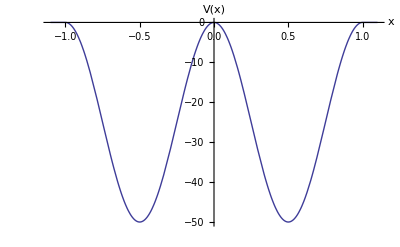

```mathematica
Plot[v[x], {x, -.55 L,.55 L}, AxesLabel-> {"x","V(x)"}]
```

Part b:

```mathematica
B=1;
```

```mathematica
ψl[x_]:=A Exp[Abs[2 en]^(1/2) x]
ψr[x_]:=B Exp[-Abs[2 en]^(1/2) x]
```

```mathematica
eqn[en_]:=ψwell''[x]+2(en-v[x])ψwell[x]
```

```mathematica
wavefuncwell[energy_]:=(en=energy;NDSolve[{eqn[energy]==0,ψwell[-L/2]==ψl[-L/2],ψwell'[-L/2]==ψl'[-L/2]},ψwell,{x,-L/2,0}])
```

```mathematica
solwell[x_?NumericQ,en_?NumericQ]:=ψwell[x]/. wavefuncwell[en][[1]]
```

```mathematica
solwellprime[x_?NumericQ,en_?NumericQ]:=ψwell'[x]/. wavefuncwell[en][[1]]
```

The above code evaluates the Schrödinger equation with the given potential function. It also solves the boundary conditions necesarry to evaluate the eigenvalues for energy as well as the wave function.

Ground State-

Because this state has even parity:

```mathematica
A=B;
```

```mathematica
eval=energy/. FindRoot[solwellprime[0,energy],{energy,-50,-49}]
```

-35.7501

Energy = -35.7501

```mathematica
efuncwell[x_]=ψwell[x]/.wavefuncwell[eval][[1]];
```

```mathematica
ψ[x_]:=efuncwell[x] /;-L/2≤x≤0
ψ[x_]:=efuncwell[-x] /;0≤x≤L/2
ψ[x_]:=ψl[x] /;x<-L/2
ψ[x_]:=ψr[x] /;x>L/2
```

```mathematica
norm=Sqrt[NIntegrate[ψ[x]^2,{x,-Infinity,Infinity}]];
```

```mathematica
ψnorm[x_]:=ψ[x]/norm
```

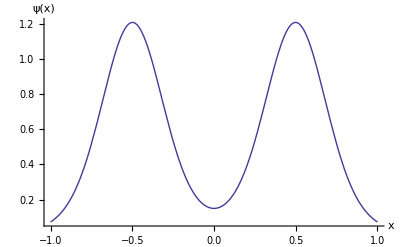

```mathematica
Plot[ψnorm[x],{x,-.5L,.5L},PlotRange->All, AxesLabel-> {"x", "ψ(x)"}]
```

```mathematica
Clear["Global`*"]
```

1st Excited State-

Because this state has odd parity:

```mathematica
A=-B;
```

```mathematica
eval=energy/. FindRoot[solwell[0,energy],{energy,-50,-49}]
```

-35.5663

Energy = -35.5663

```mathematica
ψ[x_]:=efuncwell[x] /;-L/2≤x≤0
ψ[x_]:=-efuncwell[-x] /;0≤x≤L/2
ψ[x_]:=ψl[x] /;x<-L/2
ψ[x_]:=ψr[x] /;x>L/2
```

```mathematica
norm=Sqrt[NIntegrate[ψ[x]^2,{x,-Infinity,Infinity}]];
```

```mathematica
ψnorm[x_]:=ψ[x]/norm
```

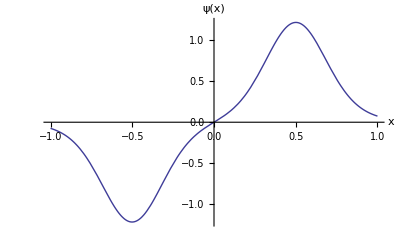

```mathematica
Plot[ψnorm[x],{x,-.5L,.5L},PlotRange->All, AxesLabel-> {"x", "ψ(x)"}]
```

2nd Excited State-

Because this state has even parity:

```mathematica
A=B;
```

```mathematica
eval=energy/. FindRoot[solwellprime[0,energy],{energy,-10,-0}]
```

-11.7515

Energy = -11.7515

```mathematica
ψ[x_]:=efuncwell[x] /;-L/2≤x≤0
ψ[x_]:=efuncwell[-x] /;0≤x≤L/2
ψ[x_]:=ψl[x] /;x<-L/2
ψ[x_]:=ψr[x] /;x>L/2
```

```mathematica
norm=Sqrt[NIntegrate[ψ[x]^2,{x,-Infinity,Infinity}]];
```

```mathematica
ψnorm[x_]:=ψ[x]/norm
```

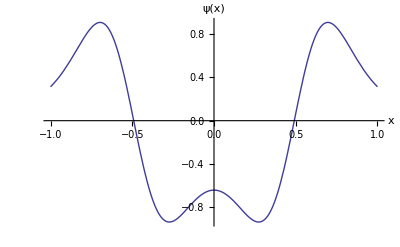

```mathematica
Plot[ψnorm[x],{x,-.5L,.5L},PlotRange->All, AxesLabel-> {"x", "ψ(x)"}]
```